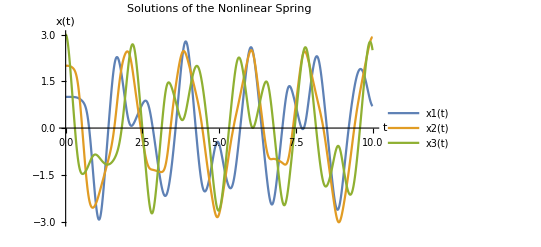

```mathematica
(* Midterm 2 Take Home Part *)
(* Name: Brandon Loptman *)
(* UID: 604-105-043 *)

Remove["Global`*"]

(*4a*)
T1= 1/2 m(x1'[t]^2+x2'[t]^2+x3'[t]^2);

V1=(1/2 k x1[t]^2+b x1[t]^4)+ (1/2 k (x2[t]- x1[t])^2+b (x2[t]- x1[t])^4)+  (1/2 k (x3[t]- x2[t])^2+b (x3[t]- x2[t])^4)+ (1/2 k (x3[t])^2+b (x3[t])^4);

lag= T1-V1;

EL[q_]:= D[lag,q]- D[ D[lag,D[q,t]],t ];

eqnlist1= List[EL[x1[t]]==0,EL[x2[t]]==0,EL[x3[t]]==0];

m=1; (*kg*)
k=1; (*kg/m*)
b=1; (*kg/m^3*)
L=1; (*m*)

ic[x_] = {x1[0]==x,x2[0]==2x,x3[0]==3x,x1'[0]==0,x2'[0]==0,x3'[0]==0};

eqnlist4=Join[eqnlist1,ic[L]];

soln1 = NDSolve[eqnlist4,{x1[t],x2[t],x3[t]},{t,0,10}];

Plot[{x1[t]/.soln1,x2[t]/.soln1,x3[t]/.soln1},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Nonlinear Spring",AxesLabel->{t,x[t]}]
```

The normal frequencies of the system are:

{√2 √(k/m),√(-((-2+√2) k)/m),√((2 k+√2 k)/m)}

The normal modes of the system are:

{{-1,0,1},{1,-√2,1},{1,√2,1}}

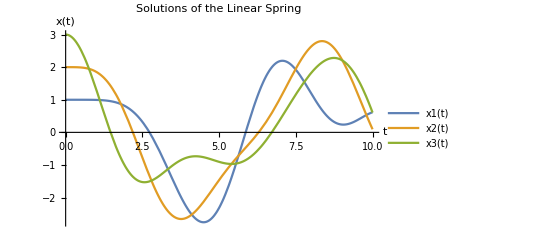

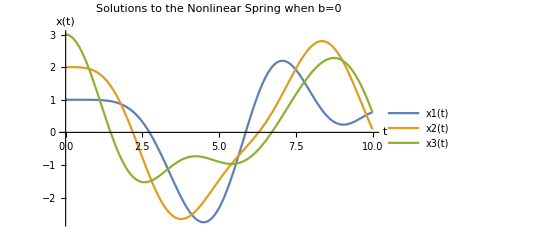

Are the two solutions the same when b=0? soln3=soln2 is...

True

```mathematica
(**************************************************************)

Clear[k,b,m]

L=1;

(* 4b *)
T2= 1/2 m(x1'[t]^2+x2'[t]^2+x3'[t]^2);

V2=1/2 k(x1[t]^2+(x2[t]-x1[t])^2+(x3[t]-x2[t])^2+x3[t]^2);

lag=T2-V2;

eqnlist2= List[EL[x1[t]]==0,EL[x2[t]]==0,EL[x3[t]]==0]//Simplify;

lag =T1-V1;
eqnlist3= List[EL[x1[t]]==0,EL[x2[t]]==0,EL[x3[t]]==0];
eqnlist3=Join[eqnlist3,ic[L]];

M = ({{m, 0, 0}, {0, m, 0}, {0, 0, m}});
K=({{2 k, k, 0}, {k, 2 k, k}, {0, k, 2 k}});
Print["The normal frequencies of the system are: "]
ω= Sqrt[Eigenvalues[{K,M}]]//FullSimplify

Print["The normal modes of the system are: "]
modes = Eigenvectors[{K,M}]

m=1; (*kg*)
k=1; (*kg/m*)
b=0; (*kg/m^3*)

eqnlist5=Join[eqnlist2,ic[L]];

soln2 = NDSolve[eqnlist5,{x1[t],x2[t],x3[t]},{t,0,10}];
soln3 = NDSolve[eqnlist3,{x1[t],x2[t],x3[t]},{t,0,10}];

Plot[{x1[t]/.soln2,x2[t]/.soln2,x3[t]/.soln2},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Linear Spring",AxesLabel->{t,x[t]}]

Plot[{x1[t]/.soln3,x2[t]/.soln3,x3[t]/.soln3},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions to the Nonlinear Spring when b=0",AxesLabel->{t,x[t]}]

Print["Are the two solutions the same when b=0? soln3=soln2 is..."]
soln3==soln2
```

Sketching a few graphs in both systems for a few inital displacement values, L.

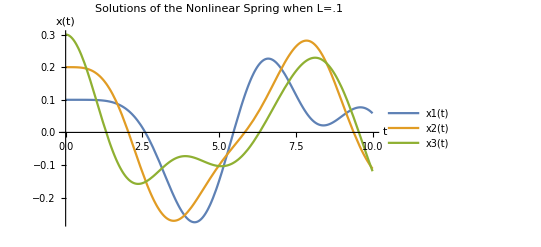

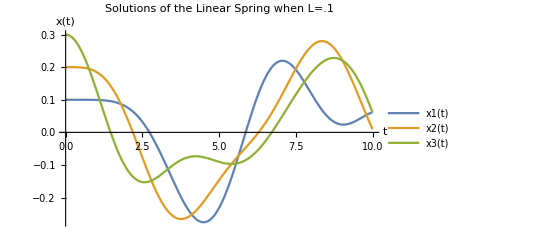

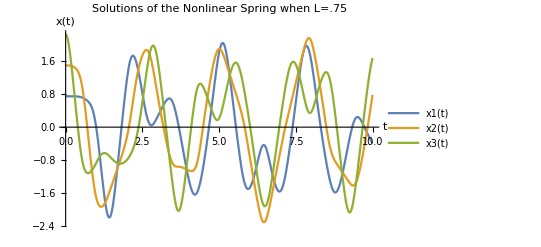

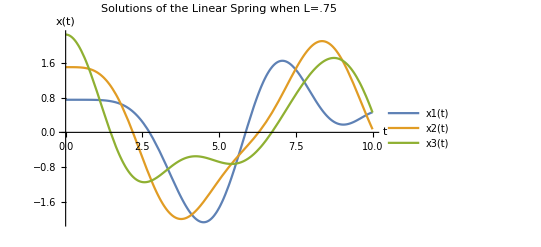

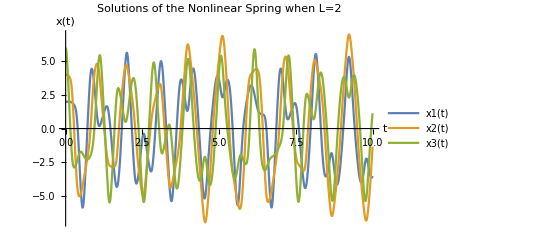

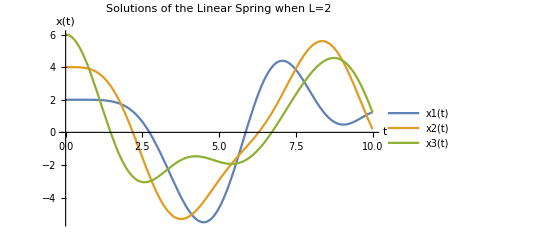

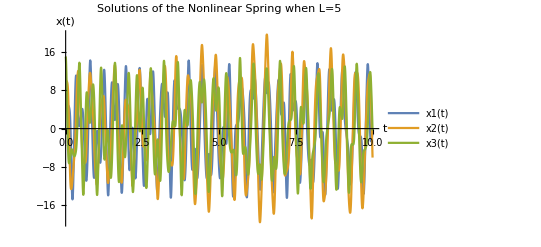

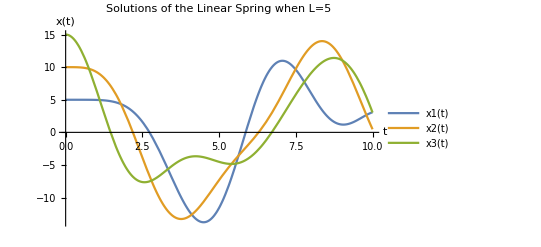

By looking at the graphs for the linear and nonlinear system as the inital displacements increase we can see that in the nonlinear case the coupling of the oscillators becomes stronger. That is, as L increases all the oscillators being to oscillate at the same frequency.

```mathematica
(**************************************************************)
Clear[L]
b=1;

(* 4c *)

Print["Sketching a few graphs in both systems for a few inital displacement values, L."]

L=.1;

eqnlist4=Join[eqnlist1,ic[L]];
soln1 = NDSolve[eqnlist4,{x1[t],x2[t],x3[t]},{t,0,10}];

eqnlist5=Join[eqnlist2,ic[L]];
soln2 = NDSolve[eqnlist5,{x1[t],x2[t],x3[t]},{t,0,10}];

Plot[{x1[t]/.soln1,x2[t]/.soln1,x3[t]/.soln1},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Nonlinear Spring when L=.1",AxesLabel->{t,x[t]}]

Plot[{x1[t]/.soln2,x2[t]/.soln2,x3[t]/.soln2},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Linear Spring when L=.1",AxesLabel->{t,x[t]}]


L=.75;

eqnlist4=Join[eqnlist1,ic[L]];
soln1 = NDSolve[eqnlist4,{x1[t],x2[t],x3[t]},{t,0,10}];

eqnlist5=Join[eqnlist2,ic[L]];
soln2 = NDSolve[eqnlist5,{x1[t],x2[t],x3[t]},{t,0,10}];

Plot[{x1[t]/.soln1,x2[t]/.soln1,x3[t]/.soln1},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Nonlinear Spring when L=.75",AxesLabel->{t,x[t]}]

Plot[{x1[t]/.soln2,x2[t]/.soln2,x3[t]/.soln2},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Linear Spring when L=.75",AxesLabel->{t,x[t]}]


L=2;

eqnlist4=Join[eqnlist1,ic[L]];
soln1 = NDSolve[eqnlist4,{x1[t],x2[t],x3[t]},{t,0,10}];

eqnlist5=Join[eqnlist2,ic[L]];
soln2 = NDSolve[eqnlist5,{x1[t],x2[t],x3[t]},{t,0,10}];

Plot[{x1[t]/.soln1,x2[t]/.soln1,x3[t]/.soln1},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Nonlinear Spring when L=2",AxesLabel->{t,x[t]}]

Plot[{x1[t]/.soln2,x2[t]/.soln2,x3[t]/.soln2},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Linear Spring when L=2",AxesLabel->{t,x[t]}]

L=5;

eqnlist4=Join[eqnlist1,ic[L]];
soln1 = NDSolve[eqnlist4,{x1[t],x2[t],x3[t]},{t,0,10}];

eqnlist5=Join[eqnlist2,ic[L]];
soln2 = NDSolve[eqnlist5,{x1[t],x2[t],x3[t]},{t,0,10}];

Plot[{x1[t]/.soln1,x2[t]/.soln1,x3[t]/.soln1},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Nonlinear Spring when L=5",AxesLabel->{t,x[t]}]

Plot[{x1[t]/.soln2,x2[t]/.soln2,x3[t]/.soln2},{t,0,10},PlotLegends->{x1[t],x2[t],x3[t]},PlotLabel->"Solutions of the Linear Spring when L=5",AxesLabel->{t,x[t]}]


Print["By looking at the graphs for the linear and nonlinear system as the inital displacements increase we can see that in the nonlinear case the coupling of the oscillators becomes stronger. That is, as L increases all the oscillators being to oscillate at the same frequency."] ;
```